## Asynchronous Updating

So this means that in general it matters in what order asynchronous updates are done, or, in effect, what “path of history” is taken.  But to get a sense of typical behavior, we can consider random sequences of updates.  Here’s an example of what one gets, doing one update per step:

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

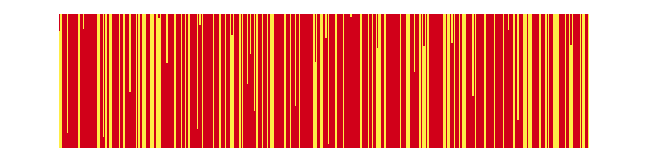

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{232,2,1},RandomChoice[{.7,.3}->{1,0},400],{100,1}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```

And here’s the corresponding result if we do 20 updates per step:

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

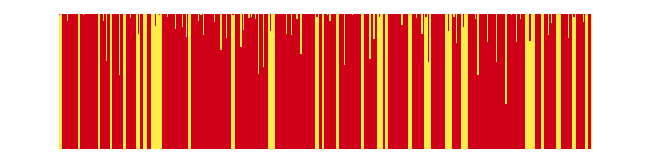

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{232,2,1},RandomChoice[{.7,.3}->{1,0},400],{100,20}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```

We might have thought that asynchronous updating would add enough randomness to “break ties” and prevent things getting stuck.  But in fact it’s not hard to see that the results are in this case in the end no different from synchronous updating.

What about for something like the GKL rule?  Here are asynchronous results for it, now with 50 updates per step (with initially 60% Hue[0.98, 1, 0.8200000000000001]):

```mathematica
caEvaluateCompiled=FunctionCompile[Function[{Typed[rule,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[rad,"MachineInteger"],Typed[init,TypeSpecifier["PackedArray"]["MachineInteger",1]],Typed[eventCount,"Integer64"]},Module[{state,position,substate,rulePart,newCellValue},

state=init;
Do[
position=RandomInteger[{1,Length[state]}];
substate=state[[Mod[#,Length[state],1] & /@ Range[position-rad,position+rad]]];
rulePart=Fold[2#1+#2&,0,substate]+1;
newCellValue=rule[[rulePart]];
state[[position]]=newCellValue;
,eventCount];
state
]]];
```

Should be compiled for all machine targets:

```mathematica
caEvaluateCompiled=CompiledCodeFunction[…];
```

```mathematica
RandomAsynchronousCellularAutomaton[{rn_,2,r_},init_,{t_,ct_}]:=NestList[caEvaluateCompiled[Reverse[IntegerDigits[rn,2,2^(2r+1)]],r,#,ct]&,init,t]
```

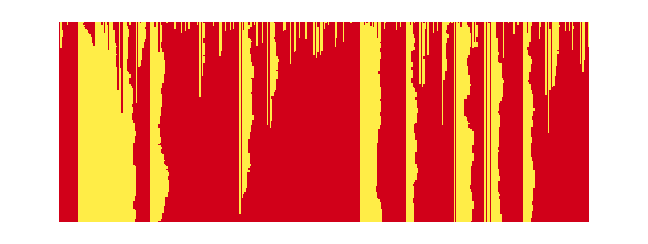

```mathematica
BlockRandom[SeedRandom[567];ArrayPlot[RandomAsynchronousCellularAutomaton[{339789091192587366278221041213531750560,2,3},RandomChoice[{.6,.4}->{1,0},400],{150,50}],ColorRules->{0->Hue[0.15, 0.72, 1],1->Hue[0.98, 1, 0.8200000000000001]},MeshStyle->Orange,Frame->None]]
```

And unlike what we saw above for synchronous updating when we added noise, the change to asynchronous updating seems to completely destroy “majority consensus” for this rule.  Note that using more updatings per step does not improve the result (which should in the end be Hue[0.98, 1, 0.8200000000000001] not Hue[0.15, 0.72, 1]):